```mathematica
Table1={{"v_(:043d), (:0441:043c)^3/с", "P, торр", "U_3, кВ"}, {100, 1.36, 0.74}, {50, 0.780, 0.66}, {25, 0.446, 0.63}, {12.5, 0.265, 0.65}, {20, 0.367, 0.64}, {30, 0.580, 0.64}, {27.5, 0.481, 0.64}, {10, 0.236, 0.65}, {5, 0.139, 0.65}}
```

{{v_н, см^3/с,P, торр,U_3, кВ},{100,1.36,0.74},{50,0.78,0.66},{25,0.446,0.63},{12.5,0.265,0.65},{20,0.367,0.64},{30,0.58,0.64},{27.5,0.481,0.64},{10,0.236,0.65},{5,0.139,0.65}}

```mathematica
Grid[Table1]
```

v_н, см^3/с | P, торр | U_3, кВ
100 | 1.36 | 0.74
50 | 0.78 | 0.66
25 | 0.446 | 0.63
12.5 | 0.265 | 0.65
20 | 0.367 | 0.64
30 | 0.58 | 0.64
27.5 | 0.481 | 0.64
10 | 0.236 | 0.65
5 | 0.139 | 0.65

```mathematica
Table2={{1.36, 0.74}, {0.78, 0.66}, {0.446, 0.63}, {0.265, 0.65}, {0.367, 0.64}, {0.58, 0.64}, {0.481, 0.64}, {0.236, 0.65}, {0.139, 0.65}}
```

{{1.36,0.74},{0.78,0.66},{0.446,0.63},{0.265,0.65},{0.367,0.64},{0.58,0.64},{0.481,0.64},{0.236,0.65},{0.139,0.65}}

{{0.139,0.65},{0.236,0.65},{0.265,0.65},{0.367,0.64},{0.446,0.63},{0.481,0.64},{0.58,0.64},{0.78,0.66},{1.36,0.74}}

0.676901-0.190741 x+0.262636 x^2-0.0648132 x^3

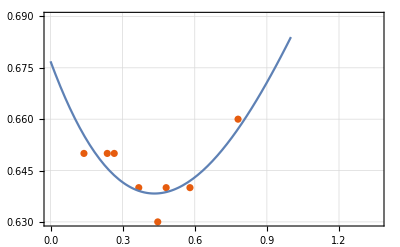

```mathematica
SortBy[Table2, Table2[[0]]]
gp1 = Fit[Table2,{1,x,x^2,x^3},x]
Show[ListPlot[SortBy[Table2,Table2[[0]]], PlotTheme->"Scientific", GridLines->Automatic ],Plot[gp1,{x,0,1}]]
```

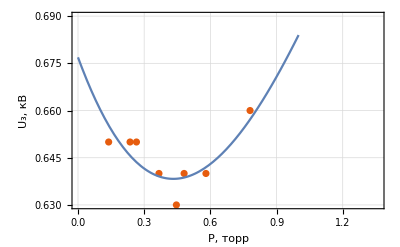

```mathematica
Show[ListPlot[SortBy[Table2,Table2[[0]]], PlotTheme->"Scientific", GridLines->Automatic ],Plot[gp1,{x,0,1}],FrameLabel->{{RawBoxes[RowBox[{SubscriptBox["U","3"],","," ","кВ"}]],None},{RawBoxes[RowBox[{"P",","," ","торр"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

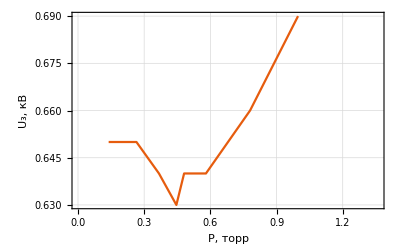
```mathematica
A1=-Graphics-
```

```mathematica
Export["/Users/alex/Desktop/MyGraph1.pdf",%34,"PDF"]
```

/Users/alex/Desktop/MyGraph1.pdf

```mathematica
Table3={{"I", "U"}, {19, 0.63}, {16.94, 0.63}, {15.08, 0.64}, {13.03, 0.64}, {10.98, 0.65}, {9.03, 0.65}, {6.99, 0.66}, {4.99, 0.68}, {3.02, 0.7}, {1.03, 0.71}}
```

{{I,U},{19,0.63},{16.94,0.63},{15.08,0.64},{13.03,0.64},{10.98,0.65},{9.03,0.65},{6.99,0.66},{4.99,0.68},{3.02,0.7},{1.03,0.71}}

```mathematica
Grid[Table3]
```

I | U
19 | 0.63
16.94 | 0.63
15.08 | 0.64
13.03 | 0.64
10.98 | 0.65
9.03 | 0.65
6.99 | 0.66
4.99 | 0.68
3.02 | 0.7
1.03 | 0.71

```mathematica
Insert[Grid[{{"I","U"},{19,0.63},{16.94,0.63},{15.08,0.64},{13.03,0.64},{10.98,0.65},{9.03,0.65},{6.99,0.66},{4.99,0.68},{3.02,0.7},{1.03,0.71}}],{Dividers->All,Spacings->1.5 {1,1}},2]
```

I | U
19 | 0.63
16.94 | 0.63
15.08 | 0.64
13.03 | 0.64
10.98 | 0.65
9.03 | 0.65
6.99 | 0.66
4.99 | 0.68
3.02 | 0.7
1.03 | 0.71

```mathematica
TeXForm[%46]
```

\begin{array}{|c|c|}
\hline
 \text{I} & \text{U} \\
\hline
 19 & 0.63 \\
\hline
 16.94 & 0.63 \\
\hline
 15.08 & 0.64 \\
\hline
 13.03 & 0.64 \\
\hline
 10.98 & 0.65 \\
\hline
 9.03 & 0.65 \\
\hline
 6.99 & 0.66 \\
\hline
 4.99 & 0.68 \\
\hline
 3.02 & 0.7 \\
\hline
 1.03 & 0.71 \\
\hline
\end{array}

```mathematica
TableG = {{19, 0.63}, {16.94, 0.63}, {15.08, 0.64}, {13.03, 0.64}, {10.98, 0.65}, {9.03, 0.65}, {6.99, 0.66}, {4.99, 0.68}, {3.02, 0.7}, {1.03, 0.71}}
```

{{19,0.63},{16.94,0.63},{15.08,0.64},{13.03,0.64},{10.98,0.65},{9.03,0.65},{6.99,0.66},{4.99,0.68},{3.02,0.7},{1.03,0.71}}

0.721572-0.00980554 x+0.000267217 x^2

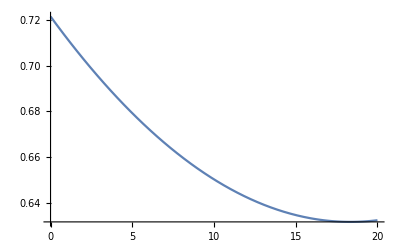

Plot::nonopt: Options expected (instead of x) beyond position 2 in Plot[gp2,{x,0,20},x]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[gp2,{x,0,20},x]].

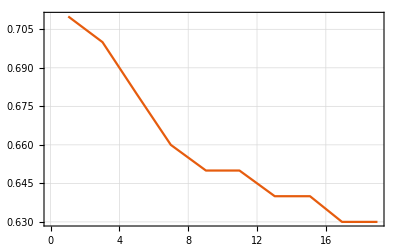
Show[-Graphics-,Plot[gp2,{x,0,20},x]]

```mathematica
gp2=Fit[TableG,{1,x,x^2},x]
Plot[gp2,{x,0,20}]
Show[ListLinePlot[TableG, PlotTheme->"Scientific", GridLines->Automatic],Plot[gp2,{x,0,20},x]]
```

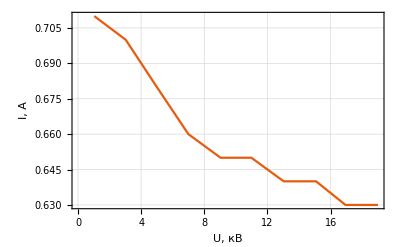

```mathematica
Show[%52,FrameLabel->{{RawBoxes[RowBox[{"I",","," ","A"}]],None},{RawBoxes[RowBox[{"U",","," ","кВ"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Table4={{"v", "P", "U_3"}, {100, 1.32, 0.48}, {50, 0.759, 0.47}, {25, 0.421, 0.42}, {12.5, 0.249, 0.41}, {6.5, 0.154, 0.43}, {11, 0.215, 0.42}, {5, 0.124, 0.44}, {20, 0.323, 0.42}, {17, 0.292, 0.41}, {15, 0.268, 0.41}}
```

{{v,P,U_3},{100,1.32,0.48},{50,0.759,0.47},{25,0.421,0.42},{12.5,0.249,0.41},{6.5,0.154,0.43},{11,0.215,0.42},{5,0.124,0.44},{20,0.323,0.42},{17,0.292,0.41},{15,0.268,0.41}}

```mathematica
TeXForm[Insert[Grid[Table4],{Dividers->All,Spacings->1.5 {1,1}},2]]
```

```mathematica
TableG2 = {{100,1.32,0.48},{50,0.759,0.47},{25,0.421,0.42},{12.5,0.249,0.41},{6.5,0.154,0.43},{11,0.215,0.42},{5,0.124,0.44},{20,0.323,0.42},{17,0.292,0.41},{15,0.268,0.41}}
```

{{100,1.32,0.48},{50,0.759,0.47},{25,0.421,0.42},{12.5,0.249,0.41},{6.5,0.154,0.43},{11,0.215,0.42},{5,0.124,0.44},{20,0.323,0.42},{17,0.292,0.41},{15,0.268,0.41}}

```mathematica
A2=Show[ListLinePlot[SortBy[TableG2,TableG2[[0]]],PlotTheme->"Scientific", GridLines->Automatic],FrameLabel->{{RawBoxes[RowBox[{SubscriptBox["U","3"],","," ","кВ"}]],None},{RawBoxes[RowBox[{"P",","," ","торр"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

SortBy::normal: Nonatomic expression expected at position 1 in SortBy[TableG2,Symbol].

ListLinePlot::lpn: SortBy[TableG2,Symbol] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gtype: ListLinePlot is not a type of graphics.

Show[ListLinePlot[SortBy[TableG2,Symbol],PlotTheme→Scientific,GridLines→Automatic],FrameLabel→{{U_3, кВ,None},{P, торр,None}},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

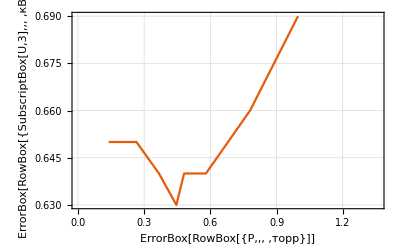

```mathematica
Show[A1,A2]
```

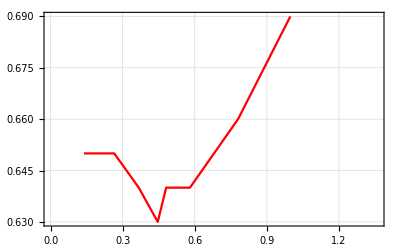

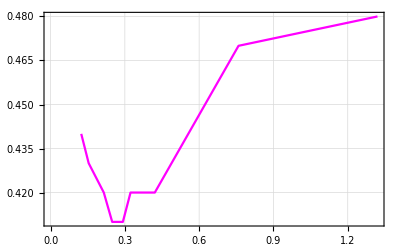

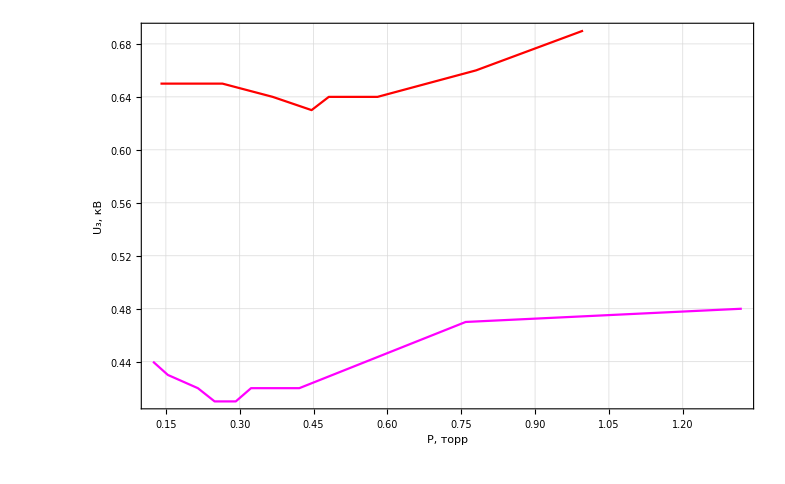

```mathematica
A1=ListLinePlot[SortBy[Table2,Table2[[0]]], PlotTheme->"Scientific", GridLines->Automatic , PlotStyle->Red]
A2=ListLinePlot[SortBy[TableG2,TableG2[[0]]],PlotTheme->"Scientific", GridLines->Automatic , PlotStyle-> Magenta]
m=Show[
A1,A2, PlotRange->All, FrameLabel->{{RawBoxes[RowBox[{SubscriptBox["U","3"],","," ","кВ"}]],None},{RawBoxes[RowBox[{"P",","," ","торр"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}
]
```

```mathematica
Table5={{"I", "U"}, {19.03, 0.41}, {17.07, 0.42}, {15.02, 0.42}, {12.99, 0.42}, {11.08, 0.42}, {9.01, 0.46}, {7.02, 0.48}, {5.01, 0.48}, {3.00, 0.49}, {1.07, 0.50}, {0.50, 0.49}}
```

{{I,U},{19.03,0.41},{17.07,0.42},{15.02,0.42},{12.99,0.42},{11.08,0.42},{9.01,0.46},{7.02,0.48},{5.01,0.48},{3.,0.49},{1.07,0.5},{0.5,0.49}}

```mathematica
Grid[Table5]
```

I | U
19.03 | 0.41
17.07 | 0.42
15.02 | 0.42
12.99 | 0.42
11.08 | 0.42
9.01 | 0.46
7.02 | 0.48
5.01 | 0.48
3. | 0.49
1.07 | 0.5
0.5 | 0.49

```mathematica
TeXForm[Insert[Grid[{{"I","U"},{19.03,0.41},{17.07,0.42},{15.02,0.42},{12.99,0.42},{11.08,0.42},{9.01,0.46},{7.02,0.48},{5.01,0.48},{3.,0.49},{1.07,0.5},{0.5,0.49}}],{Dividers->All,Spacings->1.5 {1,1}},2]]
```

\begin{array}{|c|c|}
\hline
 \text{I} & \text{U} \\
\hline
 19.03 & 0.41 \\
\hline
 17.07 & 0.42 \\
\hline
 15.02 & 0.42 \\
\hline
 12.99 & 0.42 \\
\hline
 11.08 & 0.42 \\
\hline
 9.01 & 0.46 \\
\hline
 7.02 & 0.48 \\
\hline
 5.01 & 0.48 \\
\hline
 3. & 0.49 \\
\hline
 1.07 & 0.5 \\
\hline
 0.5 & 0.49 \\
\hline
\end{array}

```mathematica
Insert[Grid[{{"I","U"},{19.03,0.41},{17.07,0.42},{15.02,0.42},{12.99,0.42},{11.08,0.42},{9.01,0.46},{7.02,0.48},{5.01,0.48},{3.,0.49},{1.07,0.5},{0.5,0.49}}],{Dividers->All,Spacings->1.5 {1,1}},2]
```

I | U
19.03 | 0.41
17.07 | 0.42
15.02 | 0.42
12.99 | 0.42
11.08 | 0.42
9.01 | 0.46
7.02 | 0.48
5.01 | 0.48
3. | 0.49
1.07 | 0.5
0.5 | 0.49

```mathematica
TableGraph2 = {{19.03, 0.41}, {17.07, 0.42}, {15.02, 0.42}, {12.99, 0.42}, {11.08, 0.42}, {9.01, 0.46}, {7.02, 0.48}, {5.01, 0.48}, {3., 0.49}, {1.07, 0.5}, {0.5, 0.49}}
```

{{19.03,0.41},{17.07,0.42},{15.02,0.42},{12.99,0.42},{11.08,0.42},{9.01,0.46},{7.02,0.48},{5.01,0.48},{3.,0.49},{1.07,0.5},{0.5,0.49}}

0.506148-0.00645235 x+3.63155×10^-6 x^3

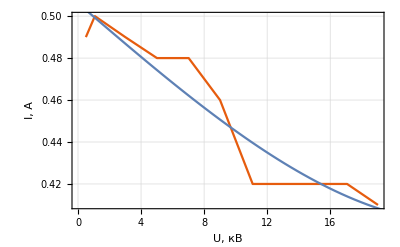

```mathematica
gp = Fit[TableGraph2,{1,x,x^3},x]
Show[ListLinePlot[TableGraph2, PlotTheme->"Scientific", GridLines->Automatic],Plot[gp,{x,0,20}],FrameLabel->{{RawBoxes[RowBox[{"I",","," ","A"}]],None},{RawBoxes[RowBox[{"U",","," ","кВ"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

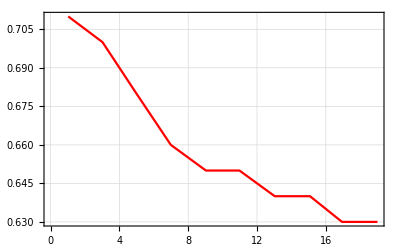

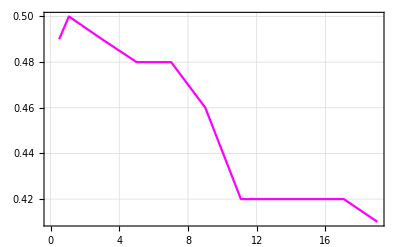

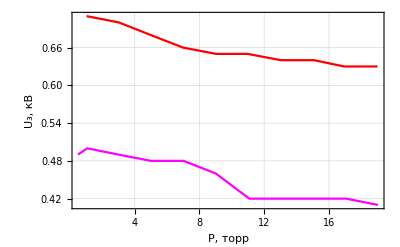

```mathematica
A1=ListLinePlot[TableG, PlotTheme->"Scientific", GridLines->Automatic,  PlotStyle->Red]
A2=ListLinePlot[TableGraph2, PlotTheme->"Scientific", GridLines->Automatic,PlotStyle->Magenta]
m=Show[
A1,A2, PlotRange->All, FrameLabel->{{RawBoxes[RowBox[{SubscriptBox["U","3"],","," ","кВ"}]],None},{RawBoxes[RowBox[{"P",","," ","торр"}]],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}
]
```